```mathematica
x^2+(x+n)^2//Expand
```

n^2+2 n x+2 x^2

```mathematica
Clear[ContractUnion]
```

```mathematica
ContractUnion[g_]:=Block[
{graphs,result,i},
graphs=Table[FormulaGraphReverse[Map[SymbolReplace[#,e]&, FindFullFormula[EdgeContract[g,e]]]],{e,EdgeList[g]}];
result=graphs[[i]];
For[i=2,i<=Length[graphs],i++,
result=GraphUnion[result,graphs[[i]]];
];
Graph[result,GraphLayout->"LayeredDigraphEmbedding", VertexLabels->"Name"]
]
```

```mathematica
$HistoryLength=10
```

10

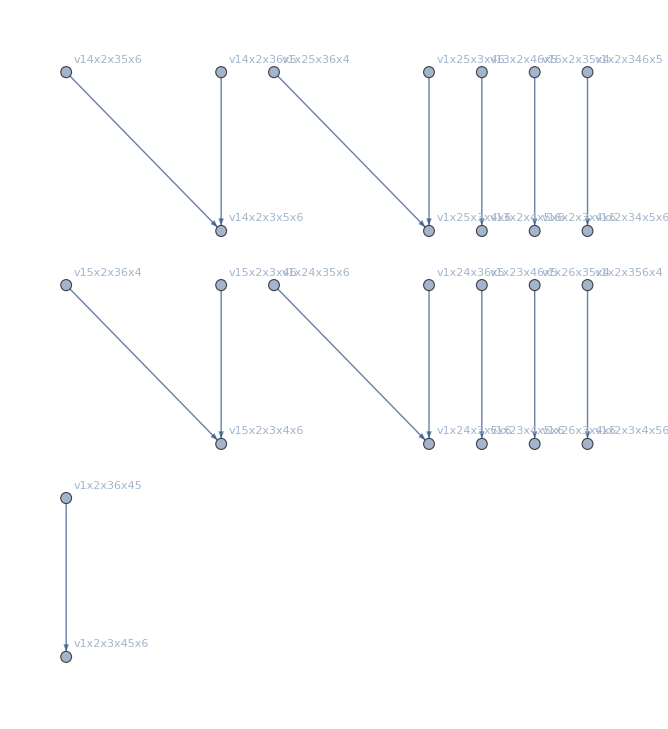

```mathematica
ContractUnion[MinimalGraph[5]]
```

```mathematica
ContractUnionLevel5[g_]:=Block[
{forms},
forms=Table[Map[SymbolReplace[#,e]&, FindFullFormula[EdgeContract[g,e]]],{e,EdgeList[g]}];
forms=Flatten[forms];
Select[forms,SymbolLevel[#]==5&]
]
```

```mathematica
Monitor[Table[(ContractUnionLevel5[MinimalGraph[k]]//Length)/2,{k,11}],k]
```

{0,0,0,0,6,27,84,230,597,1519,3858}

```mathematica
Map[FactorInteger,{0,0,0,0,6,27,84,230,597,1519,3858}]//TableForm
```

0
1 |  | 
0
1 |  | 
0
1 |  | 
0
1 |  | 
2
1 | 3
1 | 
3
3 |  | 
2
2 | 3
1 | 7
1
2
1 | 5
1 | 23
1
3
1 | 199
1 | 
7
2 | 31
1 | 
2
1 | 3
1 | 643
1